```mathematica
Quit
```

## Triángulos Numéricos

### Carga de Soluciones

```mathematica
(*Kottler*)
fKot[x_]:=1-1/x-x^2Λb/3/.Λb->1.5*10^(-32)
fUKot[u_]:=(fKot[1/u]);(*Cambio de x->1/u*)
(*Schwarzschild*)
fSch[x_]:=1-1/x
fUSch[u_]:=fSch[1/u]
```

```mathematica
(*Solucion Asimptotica*)
fAsimp[x_,λ_]:=1-(x^2 Λ)/3+(36531648 λ^2 Λ)/(x^9 (3+16 λ Λ^2)^5)+(2916 λ)/(x^6 (3+16 λ Λ^2)^3)-(1512 λ Λ)/(x^4 (3+16 λ Λ^2)^3)-3/(x (3+16 λ Λ^2))+(1536 (-(1863 λ)/(128 (3+16 λ Λ^2)^3)-(17037 λ^2 Λ^2)/(4 (3+16 λ Λ^2)^3)))/(x^7 (3+16 λ Λ^2)^2)/.Λ->1.5*10^(-32)
(*Solucion f(r) Numérico para λ=0.05*)
solY0L0P05=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_0P05_y0.txt","Table"]//Flatten;
solTL0P05=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_0P05_t.txt","Table"]//Flatten;
FunLambda0P05[x_]:=Piecewise[{{Interpolation[Transpose[{solTL0P05,solY0L0P05}]][x],x<=10.5},{fAsimp[x,0.05],x>10.5}}];
(*λ=0.1*)
solY0L0P1=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_0P1_y0.txt","Table"]//Flatten;
solTL0P1=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_0P1_t.txt","Table"]//Flatten;
FunLambda0P1[x_]:=Piecewise[{{Interpolation[Transpose[{solTL0P1,solY0L0P1}]][x],x<=10.5},{fAsimp[x,0.1],x>10.5}}];
(*λ=-1.5*)
λM15=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\Triangulos\\menos_uno_pto_cinco.dat"];
FunLambdaM1P5[x_]:=Piecewise[{
{Interpolation[λM15][x],x<=9.5},{fAsimp[x,-1.5],x>9.5}}];
(*λ=-0.05*)
λM05=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\Triangulos\\menos_cinco.dat"];
FunLambdaM0P5[x_]:=Piecewise[{
{Interpolation[λM05][x],x<=11},{fAsimp[x,-0.5],x>11}
}];
(*λ=0.05 Pero para la Masa del Sol*)
SunT=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_Sun_t.txt","Table"]//Flatten;
SunY0=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\DropBox Mine\\sol_Sun_y0.txt","Table"]//Flatten;
FunSunL0P05[x_]:=Piecewise[{{Interpolation[Transpose[{SunT,SunY0}]][x],x<=10.5},{fAsimp[x,0.05],x>10.5}}]
(*Funciones 1/u para los perfiles de f(x). Orden de λ:{-1.5,-0.5,0.05,0.1}*)
fUECG[u_]:={FunLambdaM1P5[1/u],FunLambdaM0P5[1/u],FunLambda0P05[1/u],FunLambda0P1[1/u](*,FunSunL0P05[1/u]*)}
```

### Creación de Triángulos

```mathematica
RSun=6.957*10^5(*Radio del Sol en km*);
rsSun = 2.95 (*Radio de Sch del Sol en km*);
RSun/rsSun (*Radio del Sol en radios de Sch*)
```

235831.

```mathematica
(*Para Tabla ϕmin=0.3, b1 variable, b2=1.5 b, δval=1.7, precision digitos n = 7 *)
(*Para el Sol ϕmin=03., b1=RSun/rsSun, b2=2b, δval 10^-8, precision digitos n=8*)
(*Para la tabla, con b=10, δval=10^-8, n=4, no es necesaria tanta precisión*)
```

```mathematica
Θ=0.3;(*Angle Shift*) (*Para el Sol Θ=0.2, b=RSun/rsSuun, δ=1.27,ϕmin=Θ, b2=2 b. Para fuera del sol Θ=0.3, b tu lo mueves, ϕmin=Θ, b2=1.5 b*) 
b=10 ;(*Parámetro de Impacto*) 
ϵ=1/b; (*El inverso del parámetro de Impacto*)
(*δ=1.27;(*Desplazamiento angular para los lados adyacentes*) (*Para grafico es con 1.22, para triangulos es 1.27*)*)
ϕmin=Θ; (*π/2-δ*)(*ángulo inicial para lado izquierdo*)
ϕmax=π-ϕmin;(*ángulo inicial para lado derecho*)
b2= 1.5 b ;(*Para tablas es de 1.5*)
ϵ1= 1/b2;(*parámetro de impacto de los lados adyacentes*)
δval=10^-8//N;
n=4;(*Numero de cifras significativas tomadas para la condicion inicial*)
```

#### Kottler Triangle

{{u→InterpolatingFunction[…]}}

{{u→InterpolatingFunction[…]}}

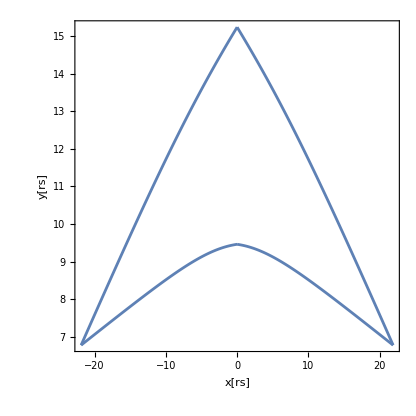

```mathematica
(*Geodesica Pricipal (Base de Triángulo)*)
u0=FindRoot[ϵ^2-fUKot[u]*u^2==0,{u,ϵ}][[1,2]] ;(*Condición donde u'[π/2]==0*)
u1=Floor[u0*10^n]/10^n//N;
(*Geodesica Pricipal (Base de Triángulo)*)
C1PhiMinKot=NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==u1},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
C1PhiMaxKot = NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==u1},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
(*Lados Adyacentes de triángulos*)
C2Kot=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinKot/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Kot = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxKot/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Ploting*)
PltC1Kot=Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxKot,{ϕ,π/2,π-Θ}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinKot,{ϕ,π/2,Θ}],PlotRange->All,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}];
PltC2Kot=ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot,{ϕ,ϕmin,π/2}];
PltC3Kot = ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3Kot,{ϕ,π/2,ϕmax}];
YLim =(( 1/u[ϕ]Sin[ϕ])*(1.001)/.C2Kot/.ϕ->π/2)[[1]]; YLimInf = (1/u[ϕ]Sin[ϕ]*(0.999)/.C1PhiMinKot/.ϕ->π/2)[[1]];
XLimL = (*((1/u[ϕ] Cos[ϕ])*(1.001)/.C3Kot/.ϕ->ϕmax)[[1]]*)27000; XLimR=-27000+0*((1/u[ϕ] Cos[ϕ])*(1.001)/.C2Kot/.ϕ->ϕmin)[[1]];
(*Plot final del triángulo*)
KotTri=Show[PltC1Kot,PltC2Kot, PltC3Kot,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}]
```

#### Schwarzschild Triangulo

```mathematica
s0=FindRoot[ϵ^2-fUSch[u]*u^2==0,{u,ϵ}][[1,2]] ;(*Condición donde u'[π/2]==0*)
s1=Floor[s0*10^n]/10^n//N;(*Condición donde u'[π/2]==0*)
(*Geodesica Pricipal (Base de Triángulo)*)
C1PhiMinSch=NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==s1},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C1PhiMaxSch = NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==s1},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Lados Adyacentes de triángulos*)
C2Sch=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinSch/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Sch = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxSch/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
```

#### Einstein Cubic Gravity Triangle

```mathematica
u0ECG=Table[FindRoot[ϵ^2-fUECG[u][[i]]*u^2==0,{u,ϵ}][[1,2]],{i,1,Length[fUECG[x]]}];
u0ECGLessPrecision=Floor[u0ECG*10^n]/10^n//N;
(*Bases del triángulo*)
C1PhiMinECG=Table[NDSolve[{(u'[ϕ])^2-ϵ^2+(fUECG[u[ϕ]])[[i]]*u[ϕ]^2==0,u[π/2+δval]==u0ECGLessPrecision[[i]]},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}]

C1PhiMaxECG = Table[NDSolve[{u'[ϕ]^2-ϵ^2+(fUECG[u[ϕ]][[i]])*u[ϕ]^2==0,u[π/2-δval]==u0ECGLessPrecision[[i]]},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];

(*Lados Adyacentes*)
C3ECG=Table[NDSolve[{(u'[ϕ])^2==ϵ1^2-(fUECG[u[ϕ]][[i]])*u[ϕ]^2,u[ϕmax]==((u[ϕ]/.C1PhiMaxECG[[i]]/.ϕ->ϕmax))[[1]]},u,{ϕ,ϕmax,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];C2ECG=Table[NDSolve[{(u'[ϕ])^2==ϵ1^2-(fUECG[u[ϕ]][[i]])*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinECG[[i]]/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];
```

{{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}}}

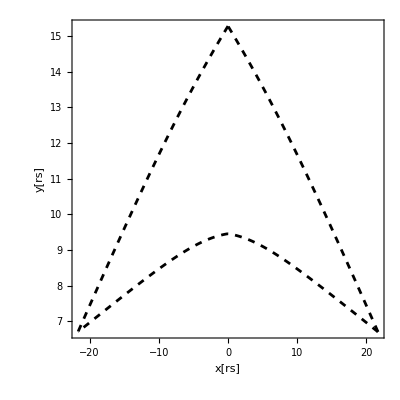
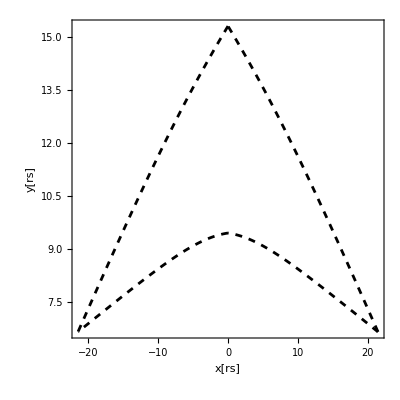
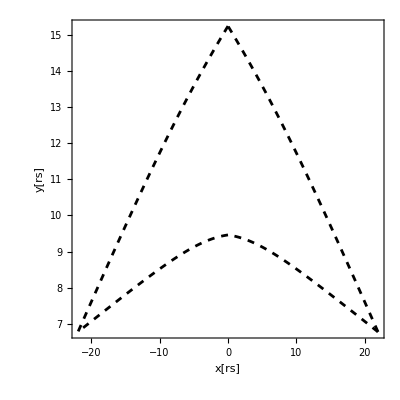
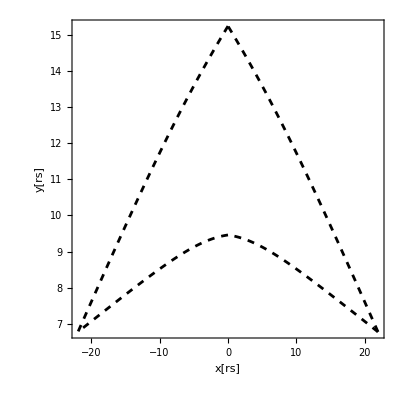

```mathematica
(*Ploting*)
PltC1ECG=Table[Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinECG[[i]],{ϕ,π/2,Θ},PlotStyle->{Black,Dashed}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxECG[[i]],{ϕ,π/2,π-Θ},PlotStyle->{Black,Dashed}],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"x[rs]","y[rs]"}],{i,1,Length[fUECG[x]]}];
PltC3ECG=Table[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3ECG[[i]],{ϕ,π/2,ϕmax},AspectRatio->1,PlotStyle->{Black,Dashed}],{i,1,Length[fUECG[x]]}];
PltC2ECG =Table[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2ECG[[i]],{ϕ,π/2,ϕmin},AspectRatio->1,PlotStyle->{Black,Dashed}],{i,1,Length[fUECG[x]]}];
xmin=Table[(1/u[ϕ] Cos[ϕ] 1.001/.C3ECG[[i]]/.ϕ->ϕmax)[[1]],{i,1,Length[fUECG[x]]}]; xmax=Table[(1/u[ϕ] Cos[ϕ] 1.001/.C2ECG[[i]]/.ϕ->ϕmin)[[1]],{i,1,Length[fUECG[x]]}];
ymin = Table[(1/u[ϕ] Sin[ϕ] 0.999 /.C1PhiMinECG/.ϕ->π/2)[[1]],{i,1,Length[fUECG[x]]}];ymax = Table[(1/u[ϕ] Sin[ϕ] 1.001 /.C2ECG/.ϕ->π/2)[[1]],{i,1,Length[fUECG[x]]}];
ECGTrian=Table[Show[PltC1ECG[[i]],PltC3ECG[[i]],PltC2ECG[[i]],AspectRatio->1(*,PlotRange->{{xmin,xmax},{ymin,ymax}}*)],{i,1,Length[fUECG[x]]}] (*Plot Final del Triángulo*)
(*ECGFunctions = {C1PhiMinECG,C1PhiMaxECG,C3ECG,C2ECG};*)
```

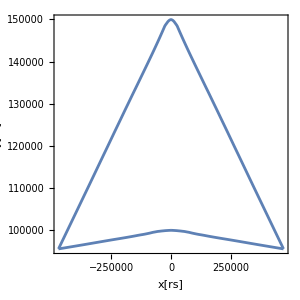
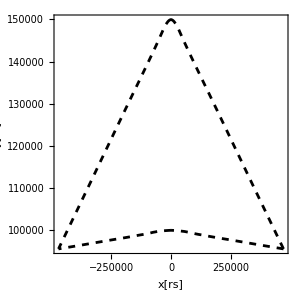
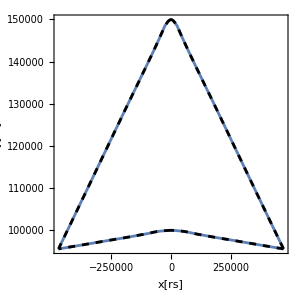
-Graphics-Kottler-Graphics-ECG-Graphics-Both Triangles

```mathematica
Row[{Labeled[Show[KotTri,ImageSize->300],Style["Kottler",16,Bold,Black],Top],Labeled[Show[ECGTrian[[1]],ImageSize->300],Style["ECG",16,Bold,Black],Top],Labeled[Show[KotTri,ECGTrian[[1]],ImageSize->300],Style["Both Triangles",16,Bold,Black],Top]},Alignment->Center]
```

### Diferencia Angular

```mathematica
(*β1=C3-C1|ϕmax  β2=C1-C2|ϕmin  β3=C2-C3|π/2*)
```

```mathematica
(*Suma Interna de Angulos Kottler*)
AngleKot[Sol_,ϕv_]:=3600*180/π (ArcTan[-u[ϕ] Sqrt[fUKot[u[ϕ]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv;
β1Kot = (AngleKot[C3Kot,ϕmax]-AngleKot[C1PhiMaxKot,ϕmax]); 
β2Kot=(AngleKot[C1PhiMinKot,ϕmin]-AngleKot[C2Kot,ϕmin]); 
β3Kot = (AngleKot[C2Kot,π/2]-AngleKot[C3Kot,π/2]); 
βsKot=β1Kot+β2Kot+β3Kot;
(*Suma interna de Angulos Schwarzschild*)
AngleSch[Sol_,ϕv_]:=3600*180/π ArcTan[-u[ϕ] Sqrt[fUSch[u[ϕ]]]D[u[ϕ],ϕ]^(-1)]/.Sol/.ϕ->ϕv;
β1Sch=AngleSch[C3Sch,ϕmax]-AngleSch[C1PhiMaxSch,ϕmax];
β2Sch=AngleSch[C1PhiMinSch,ϕmin]-AngleSch[C2Sch,ϕmin];
β3Sch=AngleSch[C2Sch,π/2]-AngleSch[C3Sch,π/2];
βsSch=β1Sch+β2Sch+β3Sch;
(*Suma Interna de Angulos ECG*)
AngleECG[Sol_,ϕv_,i_]:=3600*180/π (ArcTan[-u[ϕ] Sqrt[fUECG[u[ϕ]][[i]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv;
β1ECG=Table[AngleECG[C3ECG[[i]],ϕmax,i]-AngleECG[C1PhiMaxECG[[i]],ϕmax,i],{i,1,Length[fUECG[x]]}]//Flatten;
β2ECG=Table[AngleECG[C1PhiMinECG[[i]],ϕmin,i]-AngleECG[C2ECG[[i]],ϕmin,i],{i,1,Length[fUECG[x]]}]//Flatten;
β3ECG=Table[AngleECG[C2ECG[[i]],π/2,i]-AngleECG[C3ECG[[i]],π/2,i],{i,1,Length[fUECG[x]]}]//Flatten;
βsECG= β1ECG+β2ECG+β3ECG;
αKot=Abs[βsKot[[1]]-βsECG];(*Angular Diference*)
αSch=Abs[βsSch[[1]]-βsECG];
Print["Angular Difference with Kottler BG is: ", αKot]
Print["Angular Difference with Sch Bg is: ", αSch]
Print["Abs Difference αKot-αSch",Abs[αKot-αSch] ]
```

Angular Difference with Kottler BG is: {1812.7,3507.54,60.8721,122.292}

Angular Difference with Sch Bg is: {1812.7,3507.54,60.8721,122.292}

Abs Difference αKot-αSch{0.,0.,0.,0.}

```mathematica
αKotb10n4={1812.7035380902234,3507.536226366763,60.87206509069074,122.29219917592127};
αSchb10n4={1812.7035380902234,3507.536226366763,60.87206509069074,122.29219917592127};
Abs[αKotb10n4-αSchb10n4]
```

{0.,0.,0.,0.}

```mathematica
αKotb10={329.8252686650958,2310.596234129509,168.28403536987025,141.49983494181652};
αSchb10={329.8252686650958,2310.596234129509,168.28403536987025,141.49983494181652};
Abs[αKotb10-αSchb10]
ScientificForm[αKotb10,3]
```

{0.,0.,0.,0.}

{3.3×10^2,2.31×10^3,1.68×10^2,1.41×10^2}

```mathematica
αSchb100={0.012833714601583779,0.0042777868220582604,0.0004279155982658267,0.0008559623965993524};
αKotb100={0.012833714601583779,0.0042777868220582604,0.0004279155982658267,0.0008559623965993524};
Abs[αKotb100-αSchb100]
ScientificForm[αKotb100,3]
```

{0.,0.,0.,0.}

{1.28×10^-2,4.28×10^-3,4.28×10^-4,8.56×10^-4}

```mathematica
αKotb1000={0.00003850623033940792,3.216438926756382*^-6,3.216438926756382*^-6,3.216438926756382*^-6};
αSchb1000={0.00003850623033940792,3.216438926756382*^-6,3.216438926756382*^-6,3.216438926756382*^-6};
Abs[αKotb1000-αSchb1000]
ScientificForm[αKotb1000,3]
```

{0.,0.,0.,0.}

{3.85×10^-5,3.22×10^-6,3.22×10^-6,3.22×10^-6}

```mathematica
αKotb10k={2.0372681319713593*^-8,2.0372681319713593*^-8,2.0372681319713593*^-8,2.0372681319713593*^-8};
αSchb10k={2.0372681319713593*^-8,2.0372681319713593*^-8,2.0372681319713593*^-8,2.0372681319713593*^-8};
Abs[αKotb10k-αSchb10k]
ScientificForm[αKotb10k,3]
```

{0.,0.,0.,0.}

{2.04×10^-8,2.04×10^-8,2.04×10^-8,2.04×10^-8}

```mathematica
αKotSun=9.080395102500916*^-9 (*λ=0.05*)
αSchSun=9.080395102500916*^-9 
αKotSun-αSchSun
```

9.0804×10^-9

9.0804×10^-9

0.